# 8.2 B - Homework

```mathematica
(*#3 Find the exact area of the surface obtained by rotating the curve about the x-axis. *)
```

```mathematica
x=1/3(y^2+2)^(3/2);
```

```mathematica
(1⩽y⩽2);
```

```mathematica
Plot[x,{y,-10,10}]
```

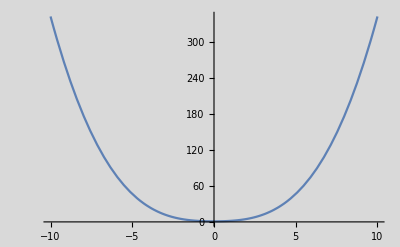

```mathematica
Show[%3,Background->LightGray]
```

```mathematica
D[x,y]
```

```mathematica
F[y_]:=y √(2+y^2);
```

```mathematica
2π∫_1^2 (y*√(1+(F[y])^2))ⅆy
```

(21 π)/2

## Problem #4

```mathematica
ClearAll[F,y,x,z,θ]
```

```mathematica
y=x^2/4-Log[x]/2;
```

```mathematica
(3⩽x⩽4);
```

```mathematica
D[y,x]
```

```mathematica
F[x_]:=-1/(2 x)+x/2
```

```mathematica
2π∫_3^4 x √(1+(F[x])^2)ⅆx
```

(40 π)/3